# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# S(t) results

## test

```mathematica
L=8;
J=1;
tlist=Table[10^i,{i,-1,10,0.0010}];
tlist//Length
```

11001

```mathematica
(*hlist=Table[(7Sqrt[5])^i,{i,-4,0,0.1}];*)
(*hlist=hlist[[1;;-1;;2]]*)
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

## plot LRN, h = 1

```mathematica
L=8;
J=1;
q=1;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_1._.m"];
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},GridLines->None,PlotRange->{All,{0,1}}],LogLinearPlot[{pageEntropy[L/2,L/2]/Log[2^(L/2)],limitzero,limitone},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed]},PlotRange->{All,{0,1}}]},Epilog->{Text[Style["g = 0",20,Blue,Bold],Scaled[{0.95,limitzero}],{36.5,1.8}],Text[Style["g = 0.63",20,Red,Bold],Scaled[{0.95,limitone}],{22.5,3}]
},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];
,{h,{1,-1}}];
(*plot=Show[plots,PlotRange->{All,{0,1}},PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]*)
```

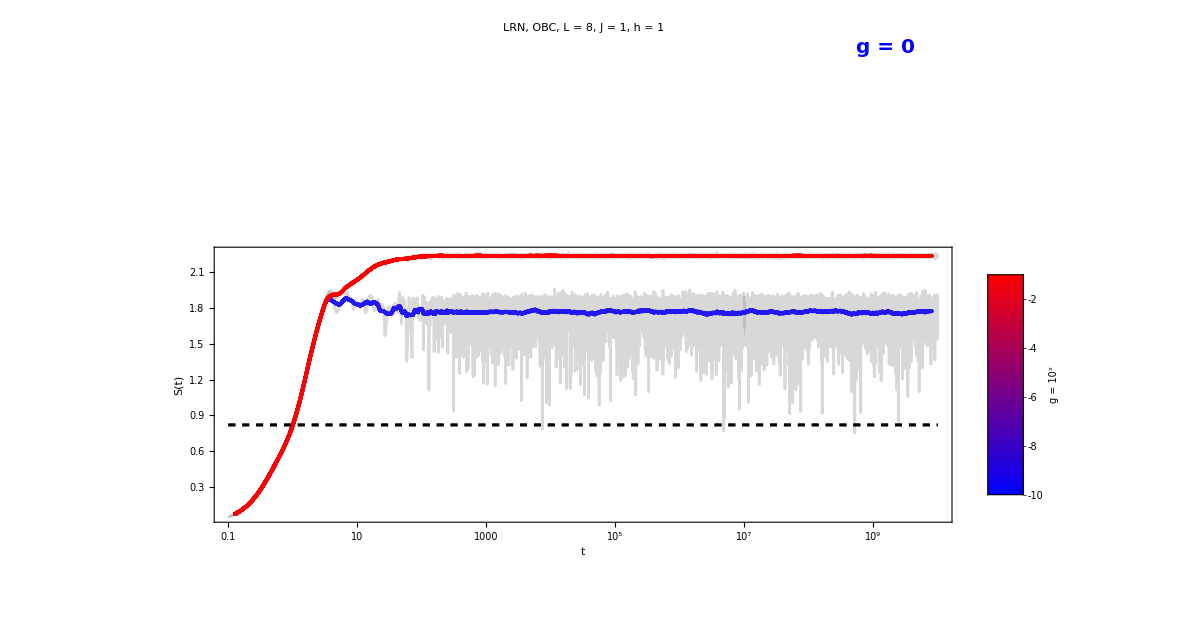

```mathematica
bar=BarLegend[{cf,{-10,-1}},LegendLabel->Style["g = \!\(\*SuperscriptBox[\(10\), \(x\)]\)",20,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400}   (*thicker=18,longer=260 px;tweak*)];
finalPlot=Legended[Show[plots,PlotRange->{All,All}],Placed[bar,Right]]
```

```mathematica
Export["L_"<>ToString[L]<>"_LRNentropy.png",finalPlot]
```

L_8_LRNentropy.png

```mathematica
value=1.95;
```

```mathematica
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

```mathematica
(*UPDATED VALUES*)
data=data[[24;;-1]];
hlist=hlist[[24;;-1]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.]],Directive[reds[[h]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1 ",40,Black],FrameLabel->{Style["t",35,Black],Rotate[Style["S(t)",35,Black],-90Degree]},GridLines->None,PlotRange->{{tlist[[1]],tlist[[-1]]},All}],LogLinearPlot[{pageEntropy[L/2,L/2],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]}]},PlotRange->{{tlist[[1]],tlist[[-1]]},All}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
bar=BarLegend[{cf,{-6,-1}},LegendLabel->Style["g",35,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400},Ticks->({#,Style[Row[{10,Superscript["",#]}],25]}&/@Range[-6,-1])];
finalPlot=Legended[Show[plots,Epilog->{Text[Style["g = 0",25,Blue,Bold],Scaled[{0.05,0.715}]],Text[Style["g = 0.1",25,Red,Bold],Scaled[{0.055,0.908}]]},PlotRange->All,ImageSize->1000],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_LRN_allplots_entropy_h_"<>ToString[q]<>"_.png",finalPlot]
```

L_8_LRN_allplots_entropy_h_1_.png

## plot LRN, h = 0.1

```mathematica
L=8;
J=1;
q=0.1;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.1_.m"];
```

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
value=1.95;
```

```mathematica
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

```mathematica
(*UPDATED VALUES*)
data=data[[9;;-7]];
hlist=hlist[[9;;-7]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.]],Directive[reds[[h]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[q],40,Black],FrameLabel->{Style["t",35,Black],Rotate[Style["S(t)",35,Black],-90Degree]},GridLines->None,PlotRange->{{tlist[[1]],tlist[[-1]]},All}],LogLinearPlot[{pageEntropy[L/2,L/2],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]}]},PlotRange->{{tlist[[1]],tlist[[-1]]},All}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
bar=BarLegend[{cf,{-9,-1}},LegendLabel->Style["g",35,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400},Ticks->({#,Style[Row[{10,Superscript["",#]}],25]}&/@Range[-9,-1])];
finalPlot=Legended[Show[plots,Epilog->{Text[Style["g = 0",25,Blue,Bold],Scaled[{0.045,0.710}]],Text[Style["g = 0.1",25,Red,Bold],Scaled[{0.055,0.880}]]},PlotRange->All,ImageSize->1000],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_LRN_allplots_entropy_h_"<>ToString[q]<>"_.png",finalPlot]
```

L_8_LRN_allplots_entropy_h_0.1_.png

## plot LRN, h = 0.3

```mathematica
L=8;
J=1;
q=0.3;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.3_.m"];
```

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
value=1.95;
```

```mathematica
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

```mathematica
(*UPDATED VALUES*)
data=data[[16;;-1]];
hlist=hlist[[16;;-6]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.]],Directive[reds[[h]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[q],40,Black],FrameLabel->{Style["t",35,Black],Rotate[Style["S(t)",35,Black],-90Degree]},GridLines->None,PlotRange->{{tlist[[1]],tlist[[-1]]},All}],LogLinearPlot[{pageEntropy[L/2,L/2],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]}]},PlotRange->{{tlist[[1]],tlist[[-1]]},All}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
bar=BarLegend[{cf,{-7,-1}},LegendLabel->Style["g",35,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400},Ticks->({#,Style[Row[{10,Superscript["",#]}],25]}&/@Range[-7,-1])];
finalPlot=Legended[Show[plots,Epilog->{Text[Style["g = 0",25,Blue,Bold],Scaled[{0.045,0.710}]],Text[Style["g = 0.1",25,Red,Bold],Scaled[{0.055,0.90}]]},PlotRange->All,ImageSize->1000],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_LRN_allplots_entropy_h_"<>ToString[q]<>"_.png",finalPlot]
```

L_8_LRN_allplots_entropy_h_0.3_.png

## plot SRN, g = 1

```mathematica
L=8;
J=1;
q=1;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\NEW SKELETON FIGURES\\SRN_L_8_h_1..m"];
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
value=0.7;
```

```mathematica
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

```mathematica
(*UPDATED VALUES*)
data=data[[27;;-1]];
hlist=hlist[[27;;-1]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.]],Directive[reds[[h]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1",40,Black],FrameLabel->{Style["t",35,Black],Rotate[Style["S(t)",35,Black],-90Degree]},GridLines->None,PlotRange->{{tlist[[1]],tlist[[-1]]},All}],LogLinearPlot[{pageEntropy[L/2,L/2],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]}]},PlotRange->{{tlist[[1]],tlist[[-1]]},All}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
bar=BarLegend[{cf,{-5,-1}},LegendLabel->Style["h",35,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400},Ticks->({#,Style[Row[{10,Superscript["",#]}],25]}&/@Range[-5,-1])];
finalPlot=Legended[Show[plots,Epilog->{Text[Style["h = 0",25,Blue,Bold],Scaled[{0.046,0.1475}]],Text[Style["h = 0.1",25,Red,Bold],Scaled[{0.055,0.870}]]},PlotRange->All,ImageSize->1000],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_SRN_allplots_entropy_g_"<>ToString[q]<>"_.png",finalPlot]
```

L_8_SRN_allplots_entropy_g_1_.png

## plot SRN, g = 2

```mathematica
L=8;
J=1;
q=2;
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\NEW SKELETON FIGURES\\SRN_L_8_h_2..m"];
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-2]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
value=0.7;
```

```mathematica
hlist=Table[10^i,{i,-10,-1,0.2}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

```mathematica
(*UPDATED VALUES*)
data=data[[27;;-1]];
hlist=hlist[[27;;-1]];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
plots={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.]],Directive[reds[[h]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 2",40,Black],FrameLabel->{Style["t",35,Black],Rotate[Style["S(t)",35,Black],-90Degree]},GridLines->None,PlotRange->{{tlist[[1]],tlist[[-1]]},All}],LogLinearPlot[{pageEntropy[L/2,L/2],limitzero,limitone,value},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Blue,Opacity[1],Dashed],Directive[Red,Opacity[1],Dashed],Directive[Brown,Opacity[1],Dashed]}]},PlotRange->{{tlist[[1]],tlist[[-1]]},All}];
AppendTo[plots,ploten];
,{h,Length[hlist]}];
```

```mathematica
bar=BarLegend[{cf,{-10,-1}},LegendLabel->Style["h",35,Black],LabelStyle->{Black,18},ColorFunctionScaling->True,LegendMarkerSize->{10,400},Ticks->({#,Style[Row[{10,Superscript["",#]}],25]}&/@Range[-10,-1])];
finalPlot=Legended[Show[plots,Epilog->{Text[Style["h = 0",25,Blue,Bold],Scaled[{0.046,0.1475}]],Text[Style["h = 0.1",25,Red,Bold],Scaled[{0.055,0.850}]]},PlotRange->All,ImageSize->1000],Placed[bar,Right]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_SRN_allplots_entropy_g_"<>ToString[q]<>"_.png",finalPlot]
```

L_8_SRN_allplots_entropy_g_2_.png

# Mix power laws

## SRN, g = 1

```mathematica
Clear[threshold];
threshold[value_,data_List]:=Module[{pos},
(*Find index of first point with S>=threshold*)
pos=FirstPosition[data[[All,2]],_?(#>=value&),Missing["NoCrossing"]];
If[pos===Missing["NoCrossing"],Missing["NoCrossing"],
data[[First[pos],1]]]
];
```

```mathematica
series = Table[MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200], {h,Length[hlist]}];
```

```mathematica
pairs=Table[{hlist[[i]],threshold[0.7,series[[i]]]},{i,Length[series]}];
Table[{i,hlist[[i]],threshold[0.7,series[[i]]]},{i,Length[series]}]//TableForm
```

1 | 0. | Missing[NoCrossing]
2 | 1.×10^-10 | Missing[NoCrossing]
3 | 1.58489×10^-10 | Missing[NoCrossing]
4 | 2.51189×10^-10 | Missing[NoCrossing]
5 | 3.98107×10^-10 | Missing[NoCrossing]
6 | 6.30957×10^-10 | Missing[NoCrossing]
7 | 1.×10^-9 | Missing[NoCrossing]
8 | 1.58489×10^-9 | Missing[NoCrossing]
9 | 2.51189×10^-9 | Missing[NoCrossing]
10 | 3.98107×10^-9 | Missing[NoCrossing]
11 | 6.30957×10^-9 | Missing[NoCrossing]
12 | 1.×10^-8 | Missing[NoCrossing]
13 | 1.58489×10^-8 | Missing[NoCrossing]
14 | 2.51189×10^-8 | Missing[NoCrossing]
15 | 3.98107×10^-8 | Missing[NoCrossing]
16 | 6.30957×10^-8 | Missing[NoCrossing]
17 | 1.×10^-7 | Missing[NoCrossing]
18 | 1.58489×10^-7 | Missing[NoCrossing]
19 | 2.51189×10^-7 | Missing[NoCrossing]
20 | 3.98107×10^-7 | Missing[NoCrossing]
21 | 6.30957×10^-7 | Missing[NoCrossing]
22 | 1.×10^-6 | Missing[NoCrossing]
23 | 1.58489×10^-6 | Missing[NoCrossing]
24 | 2.51189×10^-6 | Missing[NoCrossing]
25 | 3.98107×10^-6 | Missing[NoCrossing]
26 | 6.30957×10^-6 | Missing[NoCrossing]
27 | 0.00001 | 4.91282×10^9
28 | 0.0000158489 | 1.88508×10^9
29 | 0.0000251189 | 7.73269×10^8
30 | 0.0000398107 | 3.0153×10^8
31 | 0.0000630957 | 1.21992×10^8
32 | 0.0001 | 4.94687×10^7
33 | 0.000158489 | 1.90691×10^7
34 | 0.000251189 | 7.64418×10^6
35 | 0.000398107 | 3.00145×10^6
36 | 0.000630957 | 1.20041×10^6
37 | 0.001 | 484541.
38 | 0.00158489 | 193344.
39 | 0.00251189 | 76266.
40 | 0.00398107 | 30713.6
41 | 0.00630957 | 12004.1
42 | 0.01 | 4756.97
43 | 0.0158489 | 1955.83
44 | 0.0251189 | 747.018
45 | 0.0398107 | 305.725
46 | 0.0630957 | 121.992
47 | 0.1 | 49.355

```mathematica
ListLogLogPlot[pairs,PlotRange->All]
```

-Graphics-

```mathematica
newpairs=pairs[[27;;-1]];
```

```mathematica
pairs[[27;;-1]]//TableForm
```

0.00001 | 4.91282×10^9
0.0000158489 | 1.88508×10^9
0.0000251189 | 7.73269×10^8
0.0000398107 | 3.0153×10^8
0.0000630957 | 1.21992×10^8
0.0001 | 4.94687×10^7
0.000158489 | 1.90691×10^7
0.000251189 | 7.64418×10^6
0.000398107 | 3.00145×10^6
0.000630957 | 1.20041×10^6
0.001 | 484541.
0.00158489 | 193344.
0.00251189 | 76266.
0.00398107 | 30713.6
0.00630957 | 12004.1
0.01 | 4756.97
0.0158489 | 1955.83
0.0251189 | 747.018
0.0398107 | 305.725
0.0630957 | 121.992
0.1 | 49.355

```mathematica
ListLogLogPlot[newpairs,PlotRange->All]
```

-Graphics-

```mathematica
Sstar=0.7;
```

```mathematica
(*power-law fit:log T=log a+b log g*)
logData=Transpose[{Log[newpairs[[All,1]]],Log[newpairs[[All,2]]]}];
lm=LinearModelFit[logData,{1,z},z];
{logA,b}=lm["BestFitParameters"];
a=Exp[logA];
model[g_]:=a g^b;
```

```mathematica
{xmin,xmax}=MinMax[newpairs[[All,1]]];
fitCurve=Table[{g,model[g]},{g,xmin,xmax,(xmax-xmin)/300.}];
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0],ImagePadding->6,ImageSize->50,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style["\!\(\*SubscriptBox[\(T\), \(M\)]\) ∝"TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],30,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->3];
```

```mathematica
powerplot=ListLogLogPlot[{newpairs,fitCurve},Joined->{False,True},PlotStyle->{Black,{Red,Dashed}},ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[q],40,Black],FrameLabel->{Style["h",35,Black],Rotate[Style["\!\(\*SubscriptBox[\(T\), \(M\)]\)",35,Black],-90 Degree]},GridLines->None,PlotRange->All,Epilog->Inset[powLbl,Scaled[{0.87,0.90}]]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_SRN_powerplot_entropy_g_"<>ToString[q]<>"_.png",powerplot]
```

L_8_SRN_powerplot_entropy_g_1_.png

## SRN, g = 2

```mathematica
Clear[threshold];
threshold[value_,data_List]:=Module[{pos},
(*Find index of first point with S>=threshold*)
pos=FirstPosition[data[[All,2]],_?(#>=value&),Missing["NoCrossing"]];
If[pos===Missing["NoCrossing"],Missing["NoCrossing"],
data[[First[pos],1]]]
];
```

```mathematica
series = Table[MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200], {h,Length[hlist]}];
```

```mathematica
pairs=Table[{hlist[[i]],threshold[0.7,series[[i]]]},{i,Length[series]}];
Table[{i,hlist[[i]],threshold[0.7,series[[i]]]},{i,Length[series]}]//TableForm
```

1 | 0. | Missing[NoCrossing]
2 | 1.×10^-10 | Missing[NoCrossing]
3 | 1.58489×10^-10 | 7.30013×10^9
4 | 2.51189×10^-10 | 4.57436×10^9
5 | 3.98107×10^-10 | 2.86636×10^9
6 | 6.30957×10^-10 | 1.81272×10^9
7 | 1.×10^-9 | 1.15168×10^9
8 | 1.58489×10^-9 | 7.35074×10^8
9 | 2.51189×10^-9 | 4.55335×10^8
10 | 3.98107×10^-9 | 2.89955×10^8
11 | 6.30957×10^-9 | 1.82949×10^8
12 | 1.×10^-8 | 1.15966×10^8
13 | 1.58489×10^-8 | 7.26659×10^7
14 | 2.51189×10^-8 | 4.57436×10^7
15 | 3.98107×10^-8 | 2.87297×10^7
16 | 6.30957×10^-8 | 1.82109×10^7
17 | 1.×10^-7 | 1.15699×10^7
18 | 1.58489×10^-7 | 7.21657×10^6
19 | 2.51189×10^-7 | 4.59548×10^6
20 | 3.98107×10^-7 | 2.88623×10^6
21 | 6.30957×10^-7 | 1.82529×10^6
22 | 1.×10^-6 | 1.14639×10^6
23 | 1.58489×10^-6 | 724988.
24 | 2.51189×10^-6 | 458491.
25 | 3.98107×10^-6 | 291293.
26 | 6.30957×10^-6 | 183371.
27 | 0.00001 | 115699.
28 | 0.0000158489 | 72833.4
29 | 0.0000251189 | 45954.8
30 | 0.0000398107 | 29129.3
31 | 0.0000630957 | 18127.2
32 | 0.0001 | 11490.3
33 | 0.000158489 | 7266.59
34 | 0.000251189 | 4563.84
35 | 0.000398107 | 2879.59
36 | 0.000630957 | 1829.49
37 | 0.001 | 1154.33
38 | 0.00158489 | 718.341
39 | 0.00251189 | 459.548
40 | 0.00398107 | 289.288
41 | 0.00630957 | 182.529
42 | 0.01 | 115.433
43 | 0.0158489 | 72.4988
44 | 0.0251189 | 45.8491
45 | 0.0398107 | 28.8623
46 | 0.0630957 | 18.169
47 | 0.1 | 11.6233

```mathematica
ListLogLogPlot[pairs,PlotRange->All]
```

-Graphics-

```mathematica
newpairs=pairs[[3;;-1]];
```

```mathematica
pairs[[3;;-1]]//TableForm
```

1.58489×10^-10 | 7.30013×10^9
2.51189×10^-10 | 4.57436×10^9
3.98107×10^-10 | 2.86636×10^9
6.30957×10^-10 | 1.81272×10^9
1.×10^-9 | 1.15168×10^9
1.58489×10^-9 | 7.35074×10^8
2.51189×10^-9 | 4.55335×10^8
3.98107×10^-9 | 2.89955×10^8
6.30957×10^-9 | 1.82949×10^8
1.×10^-8 | 1.15966×10^8
1.58489×10^-8 | 7.26659×10^7
2.51189×10^-8 | 4.57436×10^7
3.98107×10^-8 | 2.87297×10^7
6.30957×10^-8 | 1.82109×10^7
1.×10^-7 | 1.15699×10^7
1.58489×10^-7 | 7.21657×10^6
2.51189×10^-7 | 4.59548×10^6
3.98107×10^-7 | 2.88623×10^6
6.30957×10^-7 | 1.82529×10^6
1.×10^-6 | 1.14639×10^6
1.58489×10^-6 | 724988.
2.51189×10^-6 | 458491.
3.98107×10^-6 | 291293.
6.30957×10^-6 | 183371.
0.00001 | 115699.
0.0000158489 | 72833.4
0.0000251189 | 45954.8
0.0000398107 | 29129.3
0.0000630957 | 18127.2
0.0001 | 11490.3
0.000158489 | 7266.59
0.000251189 | 4563.84
0.000398107 | 2879.59
0.000630957 | 1829.49
0.001 | 1154.33
0.00158489 | 718.341
0.00251189 | 459.548
0.00398107 | 289.288
0.00630957 | 182.529
0.01 | 115.433
0.0158489 | 72.4988
0.0251189 | 45.8491
0.0398107 | 28.8623
0.0630957 | 18.169
0.1 | 11.6233

```mathematica
ListLogLogPlot[newpairs,PlotRange->All]
```

-Graphics-

```mathematica
Sstar=0.7;
```

```mathematica
(*power-law fit:log T=log a+b log g*)
logData=Transpose[{Log[newpairs[[All,1]]],Log[newpairs[[All,2]]]}];
lm=LinearModelFit[logData,{1,z},z];
{logA,b}=lm["BestFitParameters"];
a=Exp[logA];
model[g_]:=a g^b;
```

```mathematica
{xmin,xmax}=MinMax[newpairs[[All,1]]];
fitCurve=Table[{g,model[g]},{g,xmin,xmax,(xmax-xmin)/300.}];
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0],ImagePadding->6,ImageSize->50,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style["\!\(\*SubscriptBox[\(T\), \(M\)]\) ∝"TraditionalForm@Superscript[g,NumberForm[b,{4,3}]],30,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->3];
```

```mathematica
powerplot=ListLogLogPlot[{newpairs,fitCurve},Joined->{False,True},PlotStyle->{Black,{Red,Dashed}},ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[q],40,Black],FrameLabel->{Style["h",35,Black],Rotate[Style["\!\(\*SubscriptBox[\(T\), \(M\)]\)",35,Black],-90 Degree]},GridLines->None,PlotRange->All,Epilog->Inset[powLbl,Scaled[{0.87,0.90}]]]
```

-Graphics-

```mathematica
Export["L_"<>ToString[L]<>"_SRN_powerplot_entropy_g_"<>ToString[q]<>"_.png",powerplot]
```

L_8_SRN_powerplot_entropy_g_2_.png